# Chapter 8 - Problem 5

```mathematica
(*Chapter 8 Problem 5 from the homework - Steph & Kelvin*)
Clear["Global`*"]
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
e = 1.60217 * 10^-19;
nano = 1 * 10^-9;
voltspernano = 1/nano;
vo = -0.5; (* original depth of the 0.5 *)
L = 2*nano; (* length of the potential well*)
Vext = 0.1; (* external bias*)
Uext = 0 - Vext;
F = Vext/L; (* electric field strength *)
```

```mathematica
zp[z_] = ((2*m)/ℏ^2)^(1/3)*(((vo - En)*e)/(e*F)^(2/3)- (e*F)^(1/3)*z);
zprime = D[zp[z],z]
```

-1.09483×10^9

```mathematica
alpha = Sqrt[(2*m*e)/ℏ^2];
k1 = alpha * Sqrt[En];
k3 = alpha *Sqrt[En - Uext];
```

```mathematica
z0 = zp[0];
zL = zp[L];
```

```mathematica
m1 = {{1,1},{I*k1, -I*k1}};
m2 = {{AiryAi[z0], AiryBi[z0]},{zprime*AiryAiPrime[z0], zprime*AiryBiPrime[z0]}};
MatrixForm[m1];
w1 = Inverse[{{1,1},{I*k1, -I*k1}}].{{AiryAi[z0], AiryBi[z0]},{zprime*AiryAiPrime[z0], zprime*AiryBiPrime[z0]}};
```

```mathematica
w2 = Inverse[{{AiryAi[zL], AiryBi[zL]},{zprime*AiryAiPrime[zL], zprime*AiryBiPrime[zL]}}].{{Exp[I*k3*L],Exp[-I*k3*L]},{I*k3*Exp[I*k3*L],-I*k3*Exp[-I*k3*L]}};
```

```mathematica
wT = w1.w2;
```

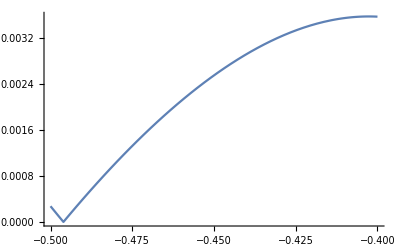

```mathematica
Plot[Abs[wT[[1,1]]],{En,-0.4,-0.5},PlotRange->All]
```

```mathematica
FindRoot[Abs[wT[[1,1]]]== 0,{En,-0.49}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{En→-0.496053}